# Glider Speed to Fly Notebook

Unit Conventions

Sink/Lift : Feet per Minute
Airspeed : Knots

```mathematica
VertSpeedToHorzSpeedConv = 101.269;
```

## Glider Polar

### Enter Glider Data Here

```mathematica
PolarData = {
{55 0.868976,-200},
{90 0.868976,-450},
{85 0.868976,-400}, 
{97.5 0.868976, -550},
{120 0.868976, -1000}
}; (* {knots airspeed, vertical speed in fpm} *)
```

### Calculate Polar

```mathematica
PolarExpression = Fit[PolarData, {1,x,x^2},x];
PolarFunction[y_] :=  PolarExpression /.x->y
```

### Glider Data

```mathematica
MinSinkSpeed = Solve[D[PolarFunction[x],x]==0,x][[1,1,2]]
```

44.778

```mathematica
MinSinkRate = PolarFunction[MinSinkSpeed]
```

-199.393

```mathematica
MaxLDspeed = Select[{a,x}/.Solve[{a == D[PolarFunction[x],x], a x == PolarFunction[x]},{a,x}], #[[2]]≥0&][[1,2]]
```

53.7518

```mathematica
MaxLDSinkRate = PolarFunction[MaxLDspeed]
```

-217.553

```mathematica
MaxLD = MaxLDspeed * VertSpeedToHorzSpeedConv / - MaxLDSinkRate (* the 101.269 is the conv from knots to fpm *)
```

25.021

### Plot Polar and Data

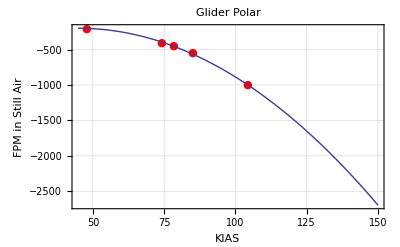

```mathematica
Show[
ListPlot[PolarData, PlotStyle->Red,PlotMarkers->{Automatic,Medium}, Frame->True, PlotRange->{0,-1000}, PlotLabel-> "Glider Polar", FrameLabel->{"KIAS","FPM in Still Air"}, GridLines-> Automatic, GridLinesStyle-> Directive[Gray,Dashed]], 
Plot[PolarFunction[x], {x,MinSinkSpeed,150}]
]
```

## McCready Speed to Fly

```mathematica
NoSinkMcCready = Table[{nextClimb, Max[MinSinkSpeed,Select[{a,x}/.Solve[{a == D[PolarFunction[x],x], a x + nextClimb == PolarFunction[x]},{a,x}], #[[2]]≥0&][[1,2]]]}, {nextClimb,0, 1000, 250}]
```

{{0,53.7518},{250,63.2286},{500,71.4595},{750,78.8356},{1000,85.5783}}

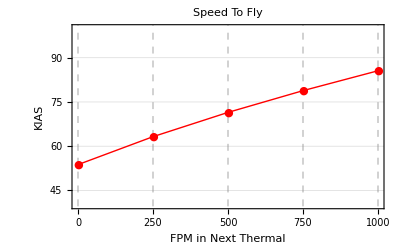

```mathematica
ListLinePlot[{NoSinkMcCready}, PlotStyle->{Red},PlotMarkers->{Automatic,Medium}, Frame->True, PlotRange->{40,100},PlotLabel-> "Speed To Fly", FrameLabel->{"FPM in Next Thermal","KIAS"}, FrameTicks -> {Table[i,{i,0,1000,250}],Automatic},GridLines-> {Table[i,{i,0,1000,250}],Automatic}, GridLinesStyle-> Directive[Gray,Dashed]]
```

## Draw Selector Ring